## Entradas

```mathematica
Ni=50;
β=10^6;       
Ci=4.88;
Di=0.43;
ηLos=10^(0.1/10);
ηNLos=10^(21/10);
VC=3 10^8;
fc=2.5 10^9;
No=2.0019 10^-12;
Ki=1;
B=50 10^6;
Lxti=0;
Lxts=500;
Lyti=0;
Lyts=500;
Lzti=0;
Lzts=100;
Lxs={500,1000};
Lys={500,500};
Lxi={0,500};
Lyi={0,0};
Lzi={0,0};
Lzs={100,100};
μx=250;
μy=250;
μz=50;
σx=100;
σy=100;
σz=25;
α =2;
```

## Xop Yop

```mathematica
jointPDF3D[Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,x_,y_,z_,μx_,μy_,μz_,σx_,σy_,σz_]:=PDF[ProductDistribution[TruncatedDistribution[{Lxti,Lxts},NormalDistribution[μx,σx]],TruncatedDistribution[{Lyti,Lyts},NormalDistribution[μy,σy]],TruncatedDistribution[{Lzti,Lzts},NormalDistribution[μz,σz]]],{x,y,z}];
di[x_,xi_,y_,yi_,z_,hi_]:=Sqrt[(xi-x)^2+(yi-y)^2+(hi-z)^2];
βeta[x_,xi_,y_,yi_,z_,hi_]:=180/π ArcSin[(hi*Sqrt[(xi-x)^2+(yi-y)^2])/(di[x,xi,y,yi,z,hi] Sqrt[(xi-x)^2+(yi-y)^2+z^2])] ;
Plos[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_]:=1/(1+Ci ⅇ^(-Di ( βeta[x,xi,y,yi,z,hi]-Ci))) ;

Li1[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_,ηLos_,ηNLos_,fc_,VC_]:=Plos[x,xi,y,yi,hi,z,Ci,Di] *((4 Pi fc)/VC)^2 *di[x,xi,y,yi,z,hi]^α *ηLos +( ηNLos *(1- Plos[x,xi,y,yi,hi,z,Ci,Di])*di[x,xi,y,yi,z,hi]^α *((4 Pi fc)/VC)^2) ;

Mi[Ni_,Lxs_,Lys_,Lxi_,Lyi_,Lzs_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_, σy_,σz_ ]:= Ni* Abs[NIntegrate[jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,μx,μy,μz,σx,σy,σz],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}]];
```

## Función Objetivo

```mathematica
ptG3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,x_,y_,z_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=(2^((β Mi[Ni,Lxs,Lys,Lxi,Lyi,Lzs,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx, σy,σz])/B)-1)*No* Li1[x,xi,y,yi,z,hi,Ci,Di,ηLos,ηNLos,fc,VC]*jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,μx,μy,μz,σx,σy,σz];

ptGNint3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=NIntegrate[ptG3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B, Ni,x,y,z,xi,yi,hi,No,ηLos,ηNLos,fc,VC],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}];
ptTotalKiUAVs3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Sum[ptGNint3D[Ci,Di,Lxs[[i]],Lys[[i]],Lzs[[i]],Lxi[[i]],Lyi[[i]],Lzi[[i]],Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xi[[All,i]],yi[[All,i]],hi[[All,i]],No,ηLos,ηNLos,fc,VC],{i,1,Ki}];
```

## Llamar a función

```mathematica
eva[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Module[{},
xMod=ptTotalKiUAVs3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xi,yi,hi,No,ηLos,ηNLos,fc,VC];
Return[xMod];
]
evaluar[Fobj_]:=Module[{fitness,total,probabilidad},
fitness=1/Fobj;
total=Total[fitness];
probabilidad=fitness/total;
probabilidad
]
```

## Función Genético

```mathematica
gene3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,No_,ηLos_,ηNLos_,fc_,VC_]:=Module[{},
Population=3000; (*populación*)
TotalCromosomas=Round[Population/1]; (*Númeor de Cromosomas*)
porCru=0.6; (*Porcentaje de cruzamiento*)
porMut=0.2; (*Porcentaje de Mutación*)
(*Matriz de Cromosomas*)
(*Dmin=ConstantArray[0,3*Ki];
Dmax=ConstantArray[200,3*Ki];*)
Dmin={0,0,10};
Dmax={900,900,300};
D1=Length[Dmin];
cromosoma=ConstantArray[0, {TotalCromosomas,D1}];
For[jj=1, jj<=D1, jj++,
cromosoma[[All,jj]]=(Dmax[[jj]]-Dmin[[jj]])*RandomReal[{0,1}, TotalCromosomas]+Dmin[[jj]];
];

Fobj=eva[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,cromosoma[[All,1;;Ki]],cromosoma[[All,Ki+1;;2*Ki]],cromosoma[[All,(2*Ki)+1;;3*Ki]],No,ηLos,ηNLos,fc,VC];
cont=1;
iter=5;
aaa=ConstantArray[0, {iter}];
While[cont<iter,
cont=cont+1;
(*Selección*)
probabilidad=evaluar[Fobj];
C11=Accumulate[probabilidad];
R=RandomReal[{0,1},{Length[cromosoma],1}];
newCromo=ConstantArray[0,Dimensions[cromosoma]];
For[i=1,i<=Length[C11],i++,
flag=0;
For[j=1,j<=Length[C11]-1,j++,
If[C11[[j]]<R[[i,1]]&&R[[i,1]]<C11[[j+1]],
newCromo[[i,All]]=cromosoma[[j+1,All]];
flag=1;
]
];
If[flag==0,
idx=Flatten[Position[C11,_?(#>R[[i,1]]&)]];
newCromo[[i,All]]=cromosoma[[idx[[1]],All]];
];
];
cromosoma=newCromo;
R=RandomReal[{0,1},{Length[cromosoma],1}];
p=1;
selecCromo=ConstantArray[0,{Length[cromosoma],Dimensions[cromosoma][[2]]}];
index=ConstantArray[0,Length[cromosoma]];
For[k=1,k<=Length[cromosoma],k++,
If[R[[k,1]]<porCru,
selecCromo[[p,All]]=cromosoma[[k,All]];
index[[p]]=k;
p=p+1;
];
];
If[p<3,
Fobj=eva[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,cromosoma[[All,1;;Ki]],cromosoma[[All,Ki+1;;2*Ki]],cromosoma[[All,(2*Ki)+1;;3*Ki]],No,ηLos,ηNLos,fc,VC];C1=RandomInteger[{1,Dimensions[cromosoma][[2]]-1},Length[index]];
cross=ConstantArray[0,{Length[selecCromo],Dimensions[selecCromo][[2]]}];
For[i=1,i<=Length[selecCromo],i++,
d=i;
If[i==Length[selecCromo],
d=0;
];
cross[[i,All]]=Join[selecCromo[[i,1;;C1[[i]]]],selecCromo[[d+1,C1[[i]]+1;;]]];
];
cromosoma[[index,All]]=cross;
(*Mutación*)
aa=Dimensions[cromosoma];
a=aa[[1]];
b=aa[[1]];
numMutation=Round[a*porMut];
values=RandomInteger[{1,a},{2,numMutation}];
values=Flatten[values];
For[jj=1,jj<=D,jj++,
cromosoma[[values,jj]]=RandomReal[Dmax[[jj]]-Dmin[[jj]],numMutation]+Dmin[[jj]];
];
];
Fobj=eva[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,cromosoma[[All,1;;Ki]],cromosoma[[All,Ki+1;;2*Ki]],cromosoma[[All,(2*Ki)+1;;3*Ki]],No,ηLos,ηNLos,fc,VC];
aaa[[cont]]=Min[Fobj];];
{fgbest,indgbest}=MinimalBy[Transpose[{Fobj,Range[Length[Fobj]]}],First][[1]];
fgbest;
cromosoma[[indgbest,All]];
Return[fgbest];
]
```

## figura

```mathematica
AbsoluteTiming[Fig3=ParallelTable[{rho,gene3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,1/rho,1/rho,σz,β,B,Ni,No,ηLos,ηNLos,fc,VC]},{rho,0.004,0.02,0.0004}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Fig3
```

{{0.004,0.0647042},{0.0044,0.0643405},{0.0048,0.0617555},{0.0052,0.0581943},{0.0056,0.0550019},{0.006,0.054807},{0.0064,0.0516784},{0.0068,0.0477518},{0.0072,0.0451536},{0.0076,0.0425996},{0.008,0.0414618},{0.0084,0.0371616},{0.0088,0.037264},{0.0092,0.0353624},{0.0096,0.0301242},{0.01,0.0283215},{0.0104,0.0275356},{0.0108,0.0272947},{0.0112,0.0237703},{0.0116,0.0208418},{0.012,0.0198884},{0.0124,0.0190603},{0.0128,0.0175701},{0.0132,0.0146709},{0.0136,0.0144704},{0.014,0.0162097},{0.0144,0.0156813},{0.0148,0.012963},{0.0152,0.0119012},{0.0156,0.0102373},{0.016,0.009764},{0.0164,0.00814419},{0.0168,0.00854581},{0.0172,0.00774081},{0.0176,0.00841267},{0.018,0.00652564},{0.0184,0.00613679},{0.0188,0.00539007},{0.0192,0.00501592},{0.0196,0.00597854},{0.02,0.00532504}}

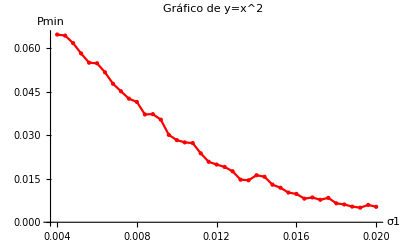

```mathematica
ListPlot[Fig3,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\Genetico-Urban1.mat",Fig3];
```

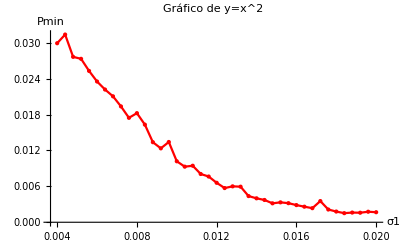

```mathematica
ListPlot[Fig3,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\Genetico-SubUrban1.mat",Fig3];
```